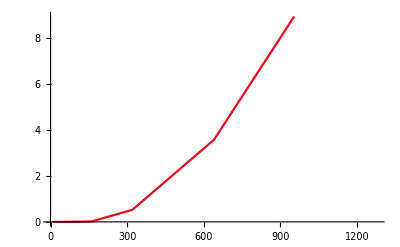
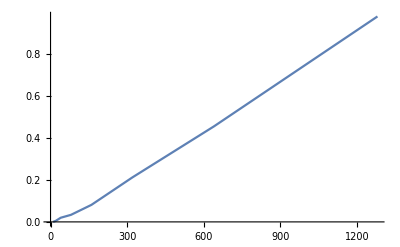
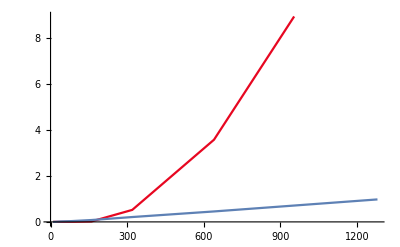
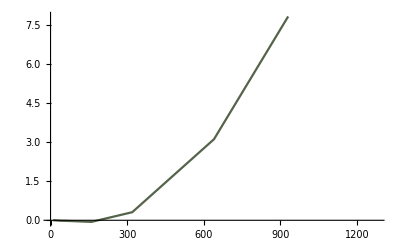

```mathematica
list1=Import["E:\\study_materials\\Finite Element Method\\Pg5\\code\\cg.txt","Table"];
list2=Import["E:\\study_materials\\Finite Element Method\\Pg5\\code\\MG.txt","Table"];
list=Table[{list1[[i,1]],list1[[i,2]]-list2[[i,2]]},{i,Length[list1]}];
img1=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img2=ListLinePlot[list2];
{img1,img2,Show[img1,img2,Range->All],ListLinePlot[list,PlotStyle->ColorData[4,"ColorList"]]}
```

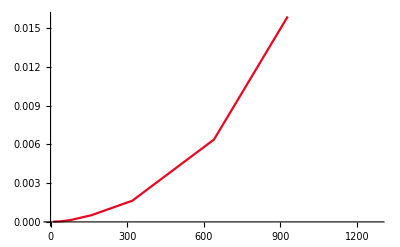
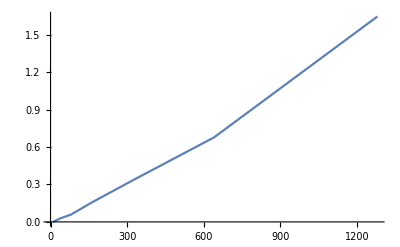
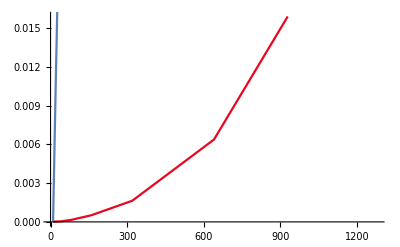
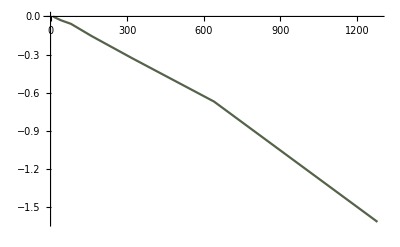

```mathematica
list1=Import["E:\\study_materials\\Finite Element Method\\Pg5\\code\\cg2.txt","Table"];
list2=Import["E:\\study_materials\\Finite Element Method\\Pg5\\code\\MG.txt","Table"];
list=Table[{list1[[i,1]],list1[[i,2]]-list2[[i,2]]},{i,Length[list1]}];
img1=ListLinePlot[list1,PlotStyle->ColorData[3,"ColorList"]];
img2=ListLinePlot[list2];
{img1,img2,Show[img1,img2,Range->All],ListLinePlot[list,PlotStyle->ColorData[4,"ColorList"]]}
```